Formulation of the nonlinear equations of motion

Guilherme Rocha Martins^a, Paulo Akira Figuti Enabe^a,Rodrigo Provasi Correia^a,Alfredo Gay Neto^a
a. Escola Politécnica, Universidade de São Paulo

This short code evaluates the nonlinear equations of motions of the reduced-order model (ROM) of a parametric excitation phenomenon.
The mainly advantage is to use the Wolphram Mathematica powerfull symbolic computation to easily identify the nondimensional quantities

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Shape functions *)
Subscript[ψ, 1][z_]:=Sin[(1 π)/L z]
Subscript[ψ, 2][z_]:=Sin[(2 π)/L z]
Subscript[ψ, 3][z_]:=Sin[(3 π)/L z]

(* Normal force over the length (z) and time (t) *)
T[z_,t_]:=Subscript[T, top]-γ*L+γ *z+EA/L Subscript[A, top] Cos[Ω t]
(* Temporal-spatial separation *)
x[z_,t_]:=Subscript[ψ, 1][z]×Subscript[A, 1][t]+Subscript[ψ, 2][z]×Subscript[A, 2][t]+Subscript[ψ, 3][z]×Subscript[A, 3][t]
```

```mathematica
(* Number that appears in some divisors *)
div:=m*Subscript[ω, 1]^2+Subscript[m, a]*Subscript[ω, 1]^2


(* Evaluate the equations of motion *)
eq1=Collect[Integrate[  ( D[x[z,t],{t,2}]+  (c Subscript[ω, 1])/div D[x[z,t],{t,1}]+EI/div D[x[z,t],{z,4}]+1/div(-γ D[x[z, t],{z,1}]-D[x[z, t],{z,2}] (Subscript[T, top]-γ L+γ z)-EA/L Subscript[A, top] Cos[Ω t] D[x[z, t],{z,2}])-d^2/div EA/(2 L) D[x[z,t],{z,2}] Integrate[(D[x[z,t],{z,1}])^2,{z,0,L}]) Subscript[ψ, 1][z] 2/L,{z,0,L}],
(*Coef. to try to collect*){(Subscript[A, 1][t])^2 Subscript[A, 2][t],(Subscript[A, 1][t])^2 Subscript[A, 3][t],(Subscript[A, 2][t])^2 Subscript[A, 3][t],Subscript[A, 1][t] (Subscript[A, 2][t])^2,Subscript[A, 1][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] Subscript[A, 3][t],Subscript[A, 1][t] Subscript[A, 2][t],Subscript[A, 1][t] Subscript[A, 3][t],
(Subscript[A, 1][t])^2,(Subscript[A, 2][t])^2,(Subscript[A, 3][t])^2,(Subscript[A, 1][t])^3,(Subscript[A, 2][t])^3,(Subscript[A, 3][t])^3,Subscript[A, 1][t],Subscript[A, 2][t],Subscript[A, 3][t],Subscript[A, 1]'[t],Subscript[A, 2]'[t],Subscript[A, 3]'[t]},FullSimplify];
eq2=Collect[Integrate[  ( D[x[z,t],{t,2}]+  (c Subscript[ω, 1])/div D[x[z,t],{t,1}]+EI/div D[x[z,t],{z,4}]+1/div(-γ D[x[z, t],{z,1}]-D[x[z, t],{z,2}] (Subscript[T, top]-γ L+γ z)-EA/L Subscript[A, top] Cos[Ω t] D[x[z, t],{z,2}])-d^2/div EA/(2 L) D[x[z,t],{z,2}] Integrate[(D[x[z,t],{z,1}])^2,{z,0,L}]) Subscript[ψ, 2][z] 2/L,{z,0,L}],
(*Coef. to try to collect*){(Subscript[A, 1][t])^2 Subscript[A, 2][t],(Subscript[A, 1][t])^2 Subscript[A, 3][t],(Subscript[A, 2][t])^2 Subscript[A, 3][t],Subscript[A, 1][t] (Subscript[A, 2][t])^2,Subscript[A, 1][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] Subscript[A, 3][t],Subscript[A, 1][t] Subscript[A, 2][t],Subscript[A, 1][t] Subscript[A, 3][t],
(Subscript[A, 1][t])^2,(Subscript[A, 2][t])^2,(Subscript[A, 3][t])^2,(Subscript[A, 1][t])^3,(Subscript[A, 2][t])^3,(Subscript[A, 3][t])^3,Subscript[A, 1][t],Subscript[A, 2][t],Subscript[A, 3][t],Subscript[A, 1]'[t],Subscript[A, 2]'[t],Subscript[A, 3]'[t]},FullSimplify];
eq3=Collect[Integrate[  ( D[x[z,t],{t,2}]+  (c Subscript[ω, 1])/div D[x[z,t],{t,1}]+EI/div D[x[z,t],{z,4}]+1/div(-γ*D[x[z, t],{z,1}]-D[x[z, t],{z,2}] (Subscript[T, top]-γ L+γ z)-EA/L Subscript[A, top] Cos[Ω t] D[x[z, t],{z,2}])-d^2/div EA/(2 L) D[x[z,t],{z,2}] Integrate[(D[x[z,t],{z,1}])^2,{z,0,L}]) Subscript[ψ, 3][z] 2/L,{z,0,L}],
(*Coef. to try to collect*){(Subscript[A, 1][t])^2 Subscript[A, 2][t],(Subscript[A, 1][t])^2 Subscript[A, 3][t],(Subscript[A, 2][t])^2 Subscript[A, 3][t],Subscript[A, 1][t] (Subscript[A, 2][t])^2,Subscript[A, 1][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] (Subscript[A, 3][t])^2,Subscript[A, 2][t] Subscript[A, 3][t],Subscript[A, 1][t] Subscript[A, 2][t],Subscript[A, 1][t] Subscript[A, 3][t],
(Subscript[A, 1][t])^2,(Subscript[A, 2][t])^2,(Subscript[A, 3][t])^2,(Subscript[A, 1][t])^3,(Subscript[A, 2][t])^3,(Subscript[A, 3][t])^3,Subscript[A, 1][t],Subscript[A, 2][t],Subscript[A, 3][t],Subscript[A, 1]'[t],Subscript[A, 2]'[t],Subscript[A, 3]'[t]},FullSimplify];
```

```mathematica
(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * 
 *  Show the equations of motion in 'Traditional form' and in 'Tex form'   *
 * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)


(* Output formatting *)
styleTitle=Style[#,FontSize->20,FontWeight->Bold,Background->LightBlue,FontFamily->"Times New Roman"]&;
styleTeX=Style[#,FontSize->20,FontWeight->Bold,Background->LightRed,FontFamily->"Times New Roman"]&;
styleText=Style[#,FontSize->16,FontWeight->Bold,FontFamily->"Times New Roman"]&;
styleEqs=Style[#,FontSize->14,FontFamily->"Cambria Math"]&;

(* Result in traditional form *)
Print[styleTitle@"Equations of motion: \n\n",
styleText@" - First equation of motion: \n",styleEqs@ TraditionalForm[eq1],"\n\n",
styleText@" - Second equation of motion: \n", styleEqs@TraditionalForm[eq2],"\n\n",
styleText@" - Third equation of motion: \n", styleEqs@TraditionalForm[eq3],"\n"
](*End print*)

Print["\n"]

(* TeX format *)
Print[styleTeX@"Equations in TeX format: \n\n",
styleText@" - First equation of motion: \n", styleEqs@TeXForm[eq1],"\n\n",
styleText@" - Second equation of motion: \n",styleEqs@ TeXForm[eq2],"\n\n",
styleText@" - Third equation of motion: \n",styleEqs@ TeXForm[eq3], "\n"
](*End print*)
```

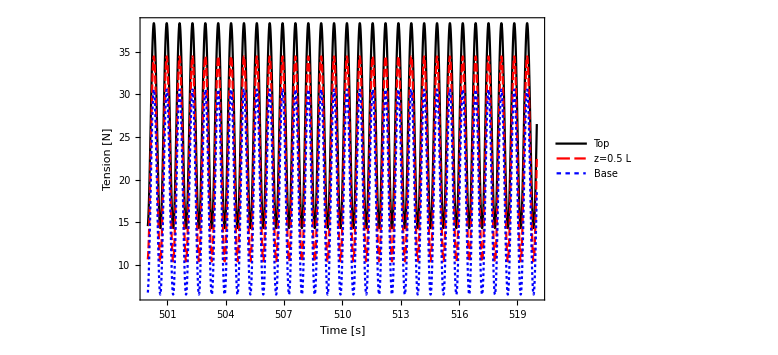

```mathematica
(**************************
 * Basic graphics formatting *
 **************************)

AxisFontSize=20;NumberSize=18;LegendFontSize=16;
font="Times New Roman";

(*Parameters of the specific problem studied*)
n=2;
Subscript[T, top]=38.4069; Ω=n*2*π*0.7555312349533149;
γ=1.19*9.81-1025*9.81*π*(22.2/1000)^2/4;
L=2.552;EA=1200;Subscript[A, top] =0.01*2.552;


Plot[{T[1,t],T[0.5,t],T[0,t]},{t,500,520},
Axes->False,Frame->True,
FrameLabel->{{Style["Tension  [N]",FontSize->AxisFontSize,FontFamily->font],None},{Style["Time  [s]",FontSize->AxisFontSize,FontFamily->font],None}},
FrameStyle->Directive[Black,FontSize->NumberSize,FontFamily->font],ImageSize->Large,
PlotStyle->{Black,{Red},{Blue},{Green}},PlotLegends->{"Top","z=0.5 L","Base"}]
```

```mathematica
Clear[d,L,g,ρ,EI,EA,m,γ,ω,ma,bool]

γ[boolWater_]:=m g-ma[boolWater] g
ma[boolWater_]:=boolWater ρ π d^2/4
ω[boolWater_,Ttop_]:=√(1/(m+ma[boolWater])(π/L)^2×(EI×(π/L)^2-1/2×γ[boolWater]×L+Ttop))
d=0.0222;g=9.81;ρ=1025;m=1.19;
L=2.552;ΔL=2.602-L;
EI=0.056;EA=1200;

(*ROM natural frequencies*)
bool=0; Tsol=Solve[ΔL==(γ[bool]×L^2)/(2 EA)+((Tt-γ[bool]×L)×L)/EA,{Tt}]; TtopAir=Tt/.Tsol[[1]]; ωROMair=ω[bool,TtopAir];
bool=1; Tsol=Solve[ΔL==(γ[bool]×L^2)/(2 EA)+((Tt-γ[bool]×L)×L)/EA,{Tt}];TtopWater=Tt/.Tsol[[1]];ωROMwater=ω[bool,TtopWater];
(*FEM natural frequencies*)
ωFEMair=√25.914433;ωFEMwater=√20.991033;(*Subscript[T, FEM,water]~=1.37s*)


(*Damping coefficients*)
ξ=0.01; (*damping of 1%*)
Print["\nDamping:\tξ = ",ξ,"\n",
"\tROM:\tc = 2ξmω = ", 2 ξ m ωROMair,"(air),\t", 2 ξ m ωROMwater,"(water)\n",
"\tFEM:\tRayleigh damping\tα = 0 and β = (2  ξ)/ω = ",(2 ξ)/ωFEMair"(air),\t", (2 ξ)/ωFEMwater,"(water)"]

Print["\n"TableForm[{
{"N",38.40687,TtopAir},
{"N",33.44049,TtopWater},
{"Hz",ωFEMair/(2 π),ωROMair/(2 π)},
{"Hz",ωFEMwater/(2 π),ωROMwater/(2 π)},
{"rad/s",ωFEMair,ωROMair},
{"rad/s",ωFEMwater,ωROMwater}},
TableHeadings->{{"T_(top, air)","T_(top, water)","f_air","f_water","ω_air","ω_water"},{"Unit","FEM","ROM"}}]]
```

Damping:	ξ = 0.01
	ROM:	c = 2ξmω = 0.130464(air),	0.112982(water)
	FEM:	Rayleigh damping	α = 0 and β = (2  ξ)/ω = 0.00392879 (air),	0.00436529(water)

| Unit | FEM | ROM
T_(top, air) | N | 38.4069 | 38.4069
T_(top, water) | N | 33.4405 | 33.4405
f_air | Hz | 0.810198 | 0.872436
f_water | Hz | 0.729184 | 0.755531
ω_air | rad/s | 5.09062 | 5.48168
ω_water | rad/s | 4.5816 | 4.74714

```mathematica
(*Conferência*)
Clear[f]
Solve[mx*9.81-1025*9.81*π*0.0222^2/4==0,mx]

frad=√(1/(1.19+1025*π*0.0222^2/4)(π/2.552)^2×(0.056 (π/2.552)^2-1/2*γ[1]*2.552+38.36));

fPRec = 10;bPRec=10;
Print["\nn=2\n",
"\tar  ","\tf= ",SetPrecision[(√25.914433)/(2*π),fPRec],"\tβ= ",SetPrecision[(2 ξ)/(√25.914433),bPRec],"\n",
"\tagua","\tf= ",SetPrecision[(√20.991033)/(2*π),fPRec],"\tβ= ",SetPrecision[(2 ξ)/(√20.991033),bPRec],

"\n\nn=4\n",
"\tar  ","\tf= ",SetPrecision[(√106.628319)/(2*π),fPRec],"\tβ= ",SetPrecision[(2 ξ)/(√106.628319),bPRec],"\n",
"\tagua","\tf= ",SetPrecision[(√85.396960)/(2*π),fPRec],"\tβ= ",SetPrecision[(2 ξ)/(√85.396960),bPRec],

"\n\nn=6\n",
"\tar  ","\tf= ",SetPrecision[(√247.002663)/(2*π),fPRec],"\tβ= ",SetPrecision[(2 ξ)/(√247.002663),bPRec],"\n",
"\tagua","\tf= ",SetPrecision[(√196.307884)/(2*π),fPRec],"\tβ= ",SetPrecision[(2 ξ)/(√196.307884),bPRec]]
```

{{mx→0.396753}}

n=2
	ar  	f= 0.8101976649	β= 0.003928792935
	agua	f= 0.7291838433	β= 0.004365289894

n=4
	ar  	f= 1.643449687	β= 0.00193683986
	agua	f= 1.470758398	β= 0.002164256798

n=6
	ar  	f= 2.501329755	β= 0.001272562666
	agua	f= 2.229918562	β= 0.001427450722

n=2
	ar  	f= 0.8101976649	β= 0.003928792935
	agua	f= 0.7291838433	β= 0.004365289894

n=4
	ar  	f= 1.643449687	β= 0.00193683986
	agua	f= 1.470758398	β= 0.002164256798

n=6
	ar  	f= 2.501329755	β= 0.001272562666
	agua	f= 2.229918562	β= 0.001427450722

,

```mathematica
√25.914433
```

5.09062